```mathematica
13/175 44100
```

3276

```mathematica
44100/(3276+Range[-5,5])
```

{44100/3271,11025/818,14700/1091,22050/1637,1764/131,175/13,44100/3277,22050/1639,14700/1093,2205/164,44100/3281}

```mathematica
Min[Numerator/@(48000/(3276+qs))]
```

293

```mathematica
qs=Table[a/b,{b,-1700,1700},{a,-b+1,b-1}]//Flatten//Union;
```

```mathematica
175*48/44.1
```

190.476

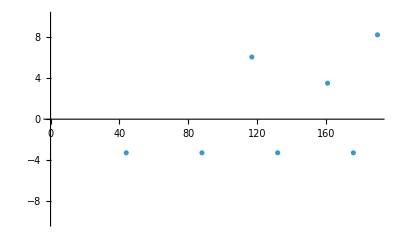

```mathematica
ListPlot[Table[48000/q Round[3276/(48000/q)]-3276,{q,1,190}],PlotRange->{-10,10}]
```

```mathematica
Round[3276/(48000/q)]/.q->{132,176,161}
```

{9,12,11}

```mathematica
48000/q Round[3276/(48000/q)]/.q->{132,176,161}+0//N
```

{3272.73,3272.73,3279.5}

```mathematica
(13+{-1 ,0,1})/175 44100
```

{3024,3276,3528}

```mathematica
(9+{-1 ,0,1})/132 48000//N
```

{2909.09,3272.73,3636.36}

```mathematica
(12+{-1 ,0,1})/176 48000//N
```

{3000.,3272.73,3545.45}

```mathematica
(11+{-1 ,0,1})/161 48000//N
```

{2981.37,3279.5,3577.64}

```mathematica
175*16/44.1
```

63.4921

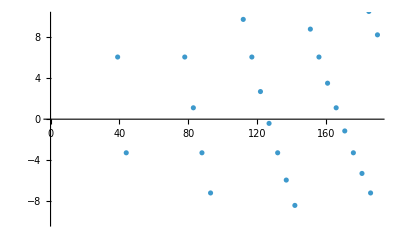

```mathematica
ListPlot[Table[16000/q Round[3276/(16000/q)]-3276,{q,1,190}],PlotRange->{-10,10}]
```

```mathematica
200*8/44.1
```

36.2812

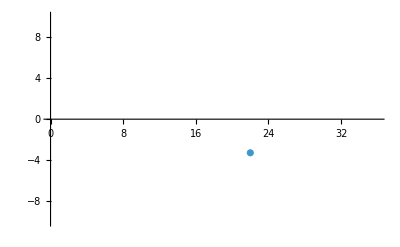

```mathematica
ListPlot[Table[8000/q Round[3276/(8000/q)]-3276,{q,1,36}],PlotRange->{-10,10}]
```

```mathematica
Round[3276/(8000/22)]
```

9

```mathematica
(9+{-1,0,1})/22 8000//N
```

{2909.09,3272.73,3636.36}

```mathematica
175/44100.
```

0.00396825

```mathematica
ChooseWindowSize[targetFreq_,sampleRate_,maxErr_:10,maxT_:0.01]:=Module[
{maxSize=Round[maxT sampleRate],err,bin,goodq},

err=Table[sampleRate/q Round[targetFreq/(sampleRate/q)]-targetFreq,{q,1,maxSize}];
goodq=Select[err,Abs[#]<=maxErr&->"Index"];
err=err[[goodq]];
bin=Round[targetFreq/(sampleRate/goodq)];
TableForm[Transpose[{goodq,goodq/sampleRate//N,bin,err//N,sampleRate/goodq(bin-1)//N,sampleRate/goodq bin//N,sampleRate/goodq(bin+1)//N}],TableHeadings->{None,{"Window size","T","Central bin n","err","f_(n - 1)","f_(n + 1)","f_(n + 1)"}}]
]
ChooseWindowSize[3276.8,44100,1]
32/44100.
```

Window size | T | Central bin n | err | f_(n - 1) | f_(n + 1) | f_(n + 1)
148 | 0.00335601 | 11 | 0.902703 | 2979.73 | 3277.7 | 3575.68
175 | 0.00396825 | 13 | -0.8 | 3024. | 3276. | 3528.
296 | 0.00671202 | 22 | 0.902703 | 3128.72 | 3277.7 | 3426.69
323 | 0.00732426 | 24 | -0.0198142 | 3140.25 | 3276.78 | 3413.31
350 | 0.00793651 | 26 | -0.8 | 3150. | 3276. | 3402.

0.000725624

```mathematica
2^15
```

32768

```mathematica
Range[23,27]/61*8000.
```

{3016.39,3147.54,3278.69,3409.84,3540.98}

```mathematica
ChooseWindowSize[3276.8,8000,10]
8000*32/44100.
6/8000.
```

Window size | T | Central bin n | err | f_(n - 1) | f_(n + 1) | f_(n + 1)
22 | 0.00275 | 9 | -4.07273 | 2909.09 | 3272.73 | 3636.36
39 | 0.004875 | 16 | 5.25128 | 3076.92 | 3282.05 | 3487.18
44 | 0.0055 | 18 | -4.07273 | 3090.91 | 3272.73 | 3454.55
56 | 0.007 | 23 | 8.91429 | 3142.86 | 3285.71 | 3428.57
61 | 0.007625 | 25 | 1.88852 | 3147.54 | 3278.69 | 3409.84
66 | 0.00825 | 27 | -4.07273 | 3151.52 | 3272.73 | 3393.94
71 | 0.008875 | 29 | -9.19437 | 3154.93 | 3267.61 | 3380.28
78 | 0.00975 | 32 | 5.25128 | 3179.49 | 3282.05 | 3384.62

5.80499

0.00075

```mathematica
w
```

```mathematica
ChooseWindowSize[3276.8,16000,4]
16000*32/44100.
12/16000.
```

Window size | T | Central bin n | err | f_(n - 1) | f_(n + 1) | f_(n + 1)
83 | 0.0051875 | 17 | 0.308434 | 3084.34 | 3277.11 | 3469.88
122 | 0.007625 | 25 | 1.88852 | 3147.54 | 3278.69 | 3409.84
127 | 0.0079375 | 26 | -1.20945 | 3149.61 | 3275.59 | 3401.57

11.61

0.00075

```mathematica
Range[15,19]/83*16000.
```

{2891.57,3084.34,3277.11,3469.88,3662.65}

```mathematica
ChooseWindowSize[3276.8,48000,10,0.005]
48000*32/44100.
32/48000.
```

Window size | T | Central bin n | err | f_(n - 1) | f_(n + 1) | f_(n + 1)
44 | 0.000916667 | 3 | -4.07273 | 2181.82 | 3272.73 | 4363.64
88 | 0.00183333 | 6 | -4.07273 | 2727.27 | 3272.73 | 3818.18
117 | 0.0024375 | 8 | 5.25128 | 2871.79 | 3282.05 | 3692.31
132 | 0.00275 | 9 | -4.07273 | 2909.09 | 3272.73 | 3636.36
161 | 0.00335417 | 11 | 2.70311 | 2981.37 | 3279.5 | 3577.64
176 | 0.00366667 | 12 | -4.07273 | 3000. | 3272.73 | 3545.45
190 | 0.00395833 | 13 | 7.41053 | 3031.58 | 3284.21 | 3536.84
191 | 0.00397917 | 13 | -9.78429 | 3015.71 | 3267.02 | 3518.32
205 | 0.00427083 | 14 | 1.24878 | 3043.9 | 3278.05 | 3512.2
220 | 0.00458333 | 15 | -4.07273 | 3054.55 | 3272.73 | 3490.91
234 | 0.004875 | 16 | 5.25128 | 3076.92 | 3282.05 | 3487.18
235 | 0.00489583 | 16 | -8.71489 | 3063.83 | 3268.09 | 3472.34

34.8299

0.000666667